# Introduction to Mathematica SS 2025.

Solve the following three exercises. Write short comments to illustrate the main steps in the code.

Vencel Szabó, pg343, Introduction to Mathematica exam solutions.

## Exercise 1. A Wimbledon simulation.

In tennis, a player wins a game if s/he has at least four points and two points more than the opponent. For instance, if the first score refers to player A who is serving and the second to the opponent, at 3-0 the game continues; at 4-1, player A wins; at 5-4 the game continues; at 6-4 player A wins, etc. Imagine now player A is serving, and s/he scores a point with probability x when s/he is serving (i.e. makes a point 100*x% of times). Realize many (eg 1000) random simulations of a game, and estimate the probability  p(x) for player A to win as a function of x. Draw a plot of p(x) for x between 0 and 1.

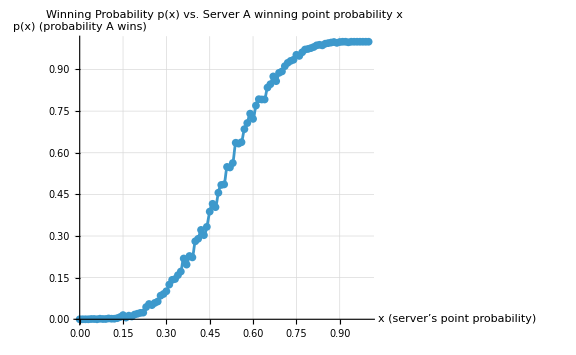

```mathematica
(* This function returns 1 if player A wins,0 if player B wins*)simulateGame[x_]:=Module[{a=0,b=0},While[True,(*A scores with probability x,otherwise B scores*)If[RandomReal[]<x,a++,b++];
(*Check for A winning:at least 4 points with a 2-point margin*)If[a>=4&&a-b>=2,Return[1]];
(*Check for B winning:at least 4 points with a  2-point margin*)If[b>=4&&b-a>=2,Return[0]];]];

(* Estimate p(x) via Monte Carlo with n simulations*)
pEstimate[x_,n_:1000]:=N[Mean@Table[simulateGame[x],{n}]];

(* Generate data points for x from 0 to 1 in steps of 0.01*)
nSims=1000;                     (*Number of simulations per x*)
step=0.01;                      (*The step size for calculating p(x)*)
data=Table[{x,pEstimate[x,nSims]},{x,0,1,step}];

(* Plot p(x) as a function of x*)
ListLinePlot[data,AxesLabel->{"x (server’s point probability)","p(x) (probability A wins)"},PlotLabel->"Winning Probability p(x) vs. Server A winning point probability x",LabelStyle->{FontFamily->"Helvetica",FontSize->14,Bold},PlotRange->{0,1},InterpolationOrder->2,GridLines->Automatic,PlotMarkers->{Automatic,8},ImageSize->Large]
```

## Exercise 2. MonteCarlo integration.

Define the function f (x) as below . Plot it in the interval (0, 3). Integrate f(x) analytically inside this range. Find numerically the maximum f_max of f(x) within the range (0,3). Write a code that generate 10^N random points uniformly distributed  in the rectangular region defined by x between (0,3) and y betwen 0 and f_max and counts how many points are below f(x). Plot the points below f(x) and the function itself for a couple values of N, e.g. N=2 and N=4 or create a Manipulate command showing the plot when varying N. The ratio of points below f(x) and the total number of random points 10^N, multiplied by the total area of the rectangular region, should approximate the exact integral of f(x) between 0 and 3 (MonteCarlo integration). Plot the result of the MonteCarlo integration as a function of N and show graphically that it converges to the  true value for N increasing from 1 to 5 or more.

```mathematica
Clear[f];f[x_]=Sin[x]^2*Exp[-x];
```

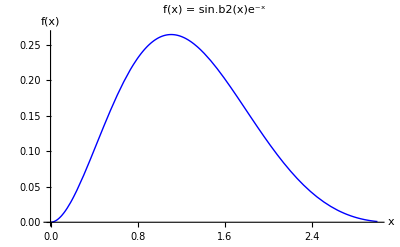

Analytical integral: 0.382669

Maximum value fmax: 0.2644

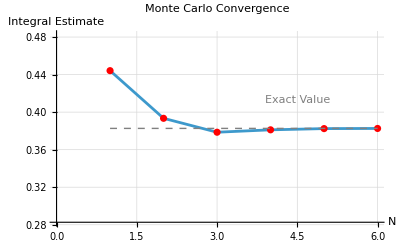

```mathematica
ClearAll["Global`*"];

f[x_]:=Sin[x]^2*Exp[-x];

(*Plot of the above function*)
Plot[f[x],{x,0,3},PlotLabel->"f(x) = sin.b2(x)e⁻ˣ",AxesLabel->{"x","f(x)"},PlotStyle->{Thick,Blue}]

(*Analytical integration*)
analyticalIntegral=Integrate[f[x],{x,0,3}];
analyticalValue=N[analyticalIntegral];
Print["Analytical integral: ",analyticalValue];

(*Finding maximum value in[0,3]*)
fmax=First@NMaximize[{f[x],0<=x<=3},x];
Print["Maximum value fmax: ",fmax];

(*Monte Carlo plotting function*)
plotMonteCarlo[n_]:=Module[{totalPoints=10^n,randomX,randomY,belowPoints,abovePoints,area=3*fmax,integralEstimate},(*Generate random points*)randomX=RandomReal[{0,3},totalPoints];
randomY=RandomReal[{0,fmax},totalPoints];
(*Separate points below and above the curve*)belowPoints=Pick[Transpose[{randomX,randomY}],UnitStep[f[randomX]-randomY],1];
abovePoints=Pick[Transpose[{randomX,randomY}],UnitStep[f[randomX]-randomY],0];
(*Based on the output of the UnitStep function the points are assigned to one of the 2 lists*)(*Calculate integral estimate*)integralEstimate=(Length[belowPoints]/totalPoints)*area;
(*Create plot*)ListPlot[{belowPoints,abovePoints},PlotStyle->{{PointSize[0.001],Green},{PointSize[0.001],Red}},PlotLabel->StringForm["N=``: {:.5f} (Exact: {:.5f})",n,integralEstimate,analyticalValue],AxesLabel->{"x","y"},ImageSize->300,Epilog->{Thick,Blue,Line[Table[{x,f[x]},{x,0,3,0.01}]]}]]

(*Monte Carlo computation function (no plot)*)
computeMonteCarlo[n_]:=Module[{totalPoints=10^n,randomX,randomY,belowCount},randomX=RandomReal[{0,3},totalPoints];
randomY=RandomReal[{0,fmax},totalPoints];
belowCount=Total[UnitStep[f[randomX]-randomY]];
(belowCount/totalPoints)*(3*fmax)]

(*Generate plots for different N values*)
Manipulate[plotMonteCarlo[n],{n,2,6,1,ControlType->Setter},ControlPlacement->Top]

(*Convergence analysis*)
convergenceData=Table[{n,Mean@Table[computeMonteCarlo[n],{10}]},(*Average 10 runs*){n,1,6}];

(*Plot convergence*)
ListPlot[convergenceData,Joined->True,Mesh->All,MeshStyle->Red,PlotRange->{Automatic,{analyticalValue-0.1,analyticalValue+0.1}},Epilog->{Dashed,Gray,Line[{{1,analyticalValue},{6,analyticalValue}}],Text["Exact Value",{4.5,analyticalValue+0.03}]},PlotLabel->"Monte Carlo Convergence",AxesLabel->{"N","Integral Estimate"},GridLines->Automatic]
```

## Exercise 3. Classical physics.

Solve the differential equation for the motion of a projectile launched from the surface of a spherical planet (without atmosphere) of mass M and radius R. The equations should be solved for the coordinates x  and y with the origin at the center of the planet. Stop the integration when the projectile hits the ground (you can use the command WhenEvent inside NDSolve). Assign as initial conditions on the surface  an initial angle θ (wrt the local horizontal), and an initial velocity v0. Plot the planet and the path. Vary θ between 30 and 90 degrees in steps of, e.g., 10 degrees, and use Manipulate to show the various trajectories.  Use the constants defined below.
Hint: if you use WhenEvent, and r[t] is the position vector, you might use this syntax to stop the integration when hitting the ground:
WhenEvent[Norm[r[t]]<R ,{tfin=t,”StopIntegration”}]
then the integration stops and tfin is the stopping time needed to draw the plots.

```mathematica
(*Constants*)
gG=6.67430*10^-11; (*gravitational constant[m^3/kg/s^2]*)
mM=5.972*10^24;     (*mass of planet (e.g.,Earth)[kg]*)
rR=6.371*10^6;      (*radius of planet (e.g.,Earth)[m]*)

(*Initial velocity, angle, and position*)
v0=8000;           (*initial speed[m/s]*)
theta=45 Degree;   (*launch angle from local horizontal*)
r0={R,0}; (* defines a vector in Cartesian coordinates,pointing from center of planet to launch point on the surface*)
```

```mathematica
ClearAll["Global`*"];

(*Constants*)
gG=6.67430*10^-11;   (*Gravitational constant[m.b3/kg/s.b2]*)
mM=5.972*10^24;      (*Mass of planet (Earth)[kg]*)
rR=6.371*10^6;       (*Radius of planet (Earth)[m]*)
v0=8000;             (*Initial velocity[m/s]*)

(*Main function to compute trajectory*)
computeTrajectory[thetaDeg_]:=Module[{thetaRad,pos0,vel0,sol,tmax,xfunc,yfunc,trajectory},thetaRad=thetaDeg*Degree;(*Convert angle to radians*)(*Initial conditions:position (surface) and velocity components*)pos0={rR,0};(*Launch from (R,0) in rectangular coordinates*)vel0=v0*{Sin[thetaRad],Cos[thetaRad]};(*{radial,tangential}*)(*Solve ODE with WhenEvent to detect reaching the Earth's surface"*)sol=First@NDSolve[{x''[t]==-gG*mM*x[t]/(x[t]^2+y[t]^2)^(3/2),y''[t]==-gG*mM*y[t]/(x[t]^2+y[t]^2)^(3/2),x[0]==pos0[[1]],y[0]==pos0[[2]],x'[0]==vel0[[1]],y'[0]==vel0[[2]],WhenEvent[Norm[{x[t],y[t]}]<=rR&&t>0,"StopIntegration"]  (*Stop when projectile hits surface*)},{x,y},{t,0,100000}];(*Max time for escape trajectories*){xfunc,yfunc}={x,y}/. sol;
tmax=(x/. sol)["Domain"][[1,2]];(*Get stopping time*)(*Create trajectory plot*)trajectory=ParametricPlot[{xfunc[t],yfunc[t]},{t,0,tmax},PlotStyle->ColorData[97][thetaDeg],PlotRange->{{-2 rR,2 rR},{-2 rR,2 rR}}];
{trajectory,tmax}];

(*Generate planet graphic*)
planet=Graphics[{LightBlue,Disk[{0,0},rR],(*Planet surface*)Gray,Circle[{0,0},rR]      (*Outline*)}];

(*Interactive visualization*)
Manipulate[Module[{result,trajectory},result=computeTrajectory[thetaDeg];
trajectory=First[result];
Show[planet,trajectory,PlotRange->{{-2 rR,2 rR},{-2 rR,2 rR}},Frame->True,Axes->False,ImageSize->500,PlotLabel->Style[StringForm["Launch angle: ``°",thetaDeg],16,Black],AspectRatio->1]],{thetaDeg,30,90,10},(*Launch angle control*)ControlPlacement->Top,TrackedSymbols:>{thetaDeg}]
```